# Celestial mechanics solutions

## Programming techniques

## Solving differential vector equations

### Typed from student sheet

{r→InterpolatingFunction[…]}

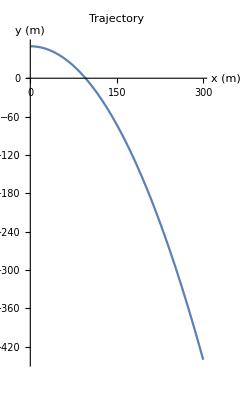

```mathematica
sol0=NDSolve[{r''[t]=={0,-9.81},r[0]=={0,50},r'[0]=={30,0}},r,{t,0,10}][[1]]
ParametricPlot[r[t]/.sol0,{t,0,10}, AxesLabel->{"x (m)","y (m)"},PlotLabel->"Trajectory"]
```

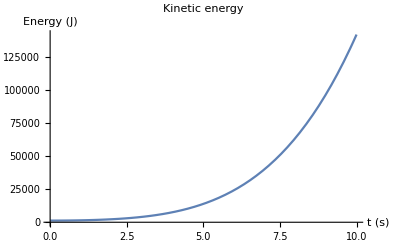

```mathematica
m=1; (* kg *)
Plot[1/2 m r[t].r[t]/.sol0,{t,0,10},AxesLabel->{"t (s)","Energy (J)"},PlotLabel->"Kinetic energy"]
```

### Answers to questions (1-3)

-Graphics-

```mathematica
a={1,2};
b={-3,4};
a*b
a.b
```

{-3,8}

5

-Graphics-

Corrected kinetic energy. In the original statement there was no prime, so position was being used instead of velocity in the calculation of kinetic energy. This is corrected by taking the derivative of the position to get the velocity. The dot product combines the x and y components into one value.

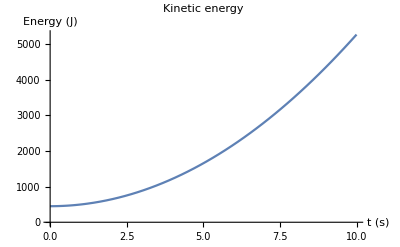

```mathematica
Plot[1/2 m r'[t].r'[t]/.sol0,{t,0,10},AxesLabel->{"t (s)","Energy (J)"},PlotLabel->"Kinetic energy"]
```

-Graphics-

Position of basketball at t = 8 s

```mathematica
r[8]/.sol0
```

{240.,-263.92}

## Conditions inside differential equations

### Typed from student sheet

{r→InterpolatingFunction[…]}

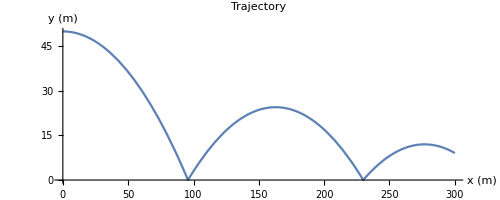

```mathematica
sol1=NDSolve[{r''[t]=={0,-9.81},r[0]=={0,50},r'[0]=={30,0},WhenEvent[r[t][[2]]==0,r'[t]->{1,-.7} r'[t]]},r,{t,0,10}][[1]]
ParametricPlot[r[t]/.sol1,{t,0,10}, AxesLabel->{"x (m)","y (m)"},PlotLabel->"Trajectory"]
```

```mathematica
sol2=NDSolve[{r''[t]=={0,-9.81},r[0]=={0,50},r'[0]=={30,0},WhenEvent[r[t][[2]]==0,hit=t;"StopIntegration"]},r,{t,0,10}][[1]]
```

{r→InterpolatingFunction[…]}

### Answers to questions (4-5)

-Graphics-

-Graphics-

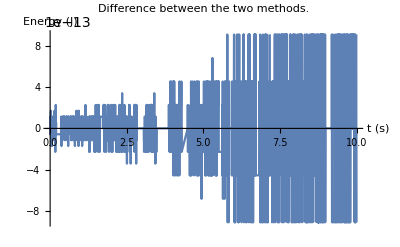

```mathematica
Plot[1/2 m Norm[r'[t]]^2/.sol0,{t,0,10},AxesLabel->{"t (s)","Energy (J)"},PlotLabel->"Kinetic energy"]
Plot[1/2 m( Norm[r'[t]]^2-r'[t].r'[t])/.sol0,{t,0,10},AxesLabel->{"t (s)","Energy (J)"},PlotLabel->"Difference between the two methods."]
```

-Graphics-

3.19275

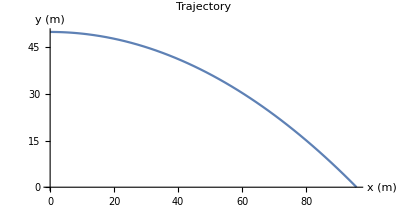

```mathematica
hit
ParametricPlot[r[t]/.sol2,{t,0,hit}, AxesLabel->{"x (m)","y (m)"},PlotLabel->"Trajectory"]
```

The [[2]] is short-form for the Part function, taking part two from expression r[t], i.e. the y coordinate. We are making an event that is triggered when the y coordinate is zero. We have integrated up to the point when the event happened and know when this happened from the value of the variable hit. We can now plot the solution to that point in time.

## Parameter variations in differential equations

### Typed from student sheet

```mathematica
pfun[a_,t_]:=Module[{sol},
sol=NDSolve[{f''[t]+a f[t]==0,f[0]==1,f'[0]==0},f,{t,0,10}][[1]];
f[t]/.sol]

Plot[pfun[2,t],{t,0,10},AxesLabel->{"t (arb.u.)","position (arb.u.)"},PlotLabel->"f(t)"]
```

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

ReplaceAll::reps: {2 f[0.000204286]+f''[0.000204286]==0,f[0]==1,f'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {2. f[0.000204286]+f''[0.000204286]==0.,f[0.]==1.,f'[0.]==0.} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.204286 cannot be used as a variable.

ReplaceAll::reps: {2 f[0.204286]+f''[0.204286]==0,f[0]==1,f'[0]==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.408368 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-

### Answers to questions (6-8)

-Graphics-

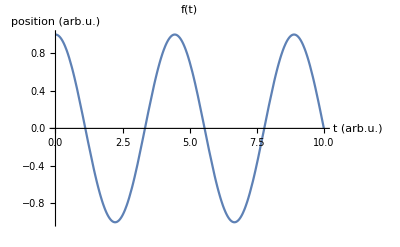

```mathematica
Plot[pfun[2,t]//Evaluate,{t,0,10},AxesLabel->{"t (arb.u.)","position (arb.u.)"},PlotLabel->"f(t)"]
```

```mathematica
pfun[a_,t_]:=Module[{sol},
sol=NDSolve[{f''[τ]+a f[τ]==0,f[0]==1,f'[0]==0},f,{τ,0,10}][[1]];
f[t]/.sol]

Plot[pfun[2,t],{t,0,10},AxesLabel->{"t (arb.u.)","position (arb.u.)"},PlotLabel->"f(t)"]
```

-Graphics-

-Graphics-

```mathematica
Manipulate[Plot[pfun[a,t]//Evaluate,{t,0,10},AxesLabel->{"t (arb.u.)","position (arb.u.)"},PlotLabel->"f(t)"],{a,0.5,3}]
```

## Special plots

### Typed from student sheet

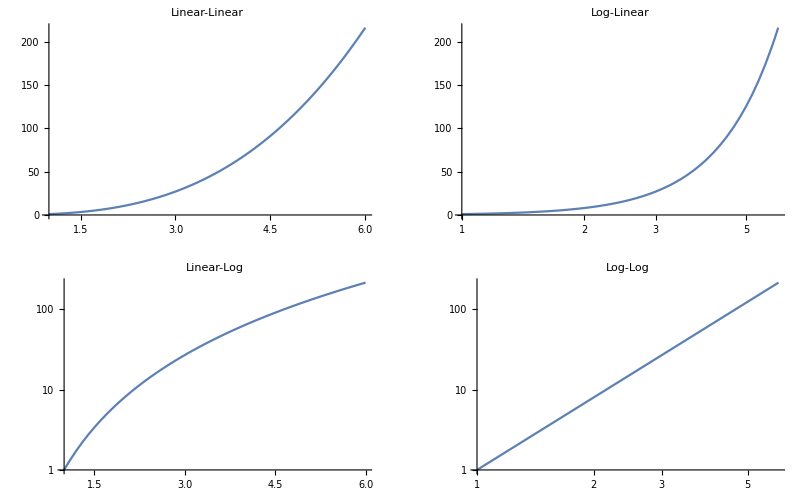

```mathematica
g[x_]:=x^3
GraphicsGrid[{{Plot[g[x],{x,1,6},PlotLabel->"Linear-Linear"],LogLinearPlot[g[x],{x,1,6},PlotLabel->"Log-Linear"]},{LogPlot[g[x],{x,1,6},PlotLabel->"Linear-Log"],LogLogPlot[g[x],{x,1,6},PlotLabel->"Log-Log"]}}]
```

### Answers to questions (9)

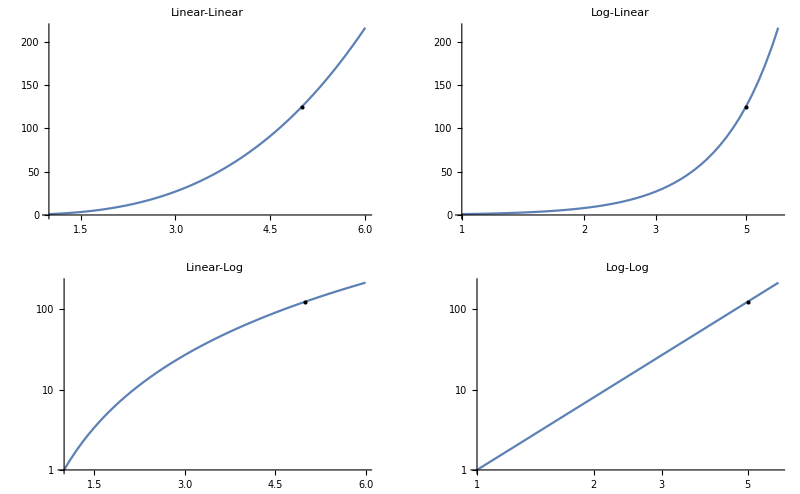

```mathematica
GraphicsGrid[{{
Plot[g[x],{x,1,6},Epilog ->Point[{5,125}],PlotLabel->"Linear-Linear"],
LogLinearPlot[g[x],{x,1,6},Epilog ->Point[{Log[5],125}],PlotLabel->"Log-Linear"]},{
LogPlot[g[x],{x,1,6},Epilog ->Point[{5,Log[125]}],PlotLabel->"Linear-Log"],
LogLogPlot[g[x],{x,1,6},Epilog ->Point[Log[{5,125}]],PlotLabel->"Log-Log"]}}]
```

You have modify the position of the point in the epilog to take cognisance of the scaling on the axes, e.g. if the y-axis has a log scale, then you need to take the log of the y position of the epilog point.

## Fitting data

### Typed from student sheet

{a0→50.4648,a1→0.0327377,a2→-4.92573}

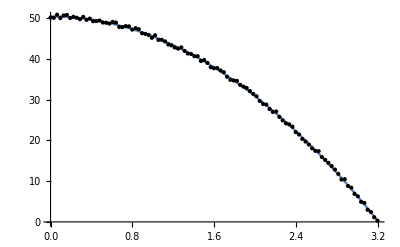

```mathematica
ypos=Table[{t,RandomReal[]+(r[t]/.sol1)[[2]]},{t,0,hit,hit/100}];
model=a0+a1 t+a2 t^2;
fit=FindFit[ypos,model,{a0,a1,a2},t]
Plot[model/.fit,{t,0,hit},Epilog->Point[ypos]]
```

### Answers to questions (10)

-Graphics-

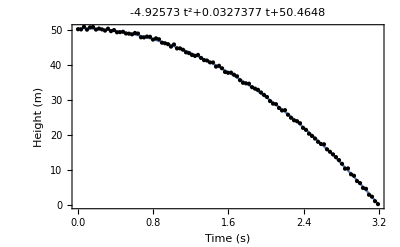

```mathematica
Plot[model/.fit,{t,0,hit},Epilog->Point[ypos], PlotLabel->(model/.fit),FrameLabel->{"Time (s)","Height (m)"},Frame->True]
```

## Study

-Graphics-

## Solving the equation of motion

```mathematica
year=24*3600*365.25; (* one year in seconds *)
G=6.6725*10^-11; (* m^3/(kg s^2) *)
au=149597870700; (* m *)
ms=1.989×10^30; (* mass of Sun in kg *)
me=5.972×10^24;  (* mass of Earth in kg *)

earthTraj=NDSolve[{
 pe''[t]== - G ms /Norm[pe[t]]^2 pe[t]/Norm[pe[t]],
pe[0]=={au,0},
pe'[0]=={0,29785.1}},pe,{t,0,3 year}][[1]]
```

{pe→InterpolatingFunction[…]}

-Graphics-

## Visualising the orbits

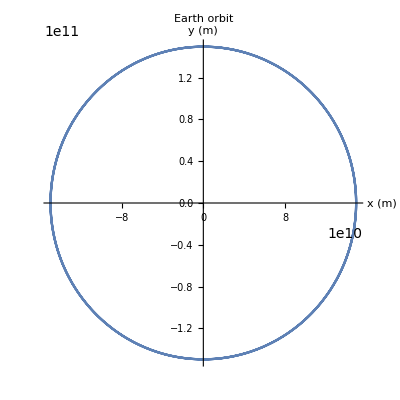

```mathematica
earthOrbit=ParametricPlot[pe[t]/.earthTraj,{t,0,3year},AspectRatio->Automatic,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Earth orbit",PlotRange->1.5*10^11]
radE=6400 500*1000; (* arbitrary units to make it visible *)
radS=10 700000*1000;(* arbitrary units to make it visible *)

Animate[Show[
earthOrbit,
Graphics[{
RGBColor[1,1,0],
Disk[{0,0},radS],
RGBColor[0,0,1],
Disk[pe[t]/.earthTraj,radE]},Axes->True]],
{t,0,year}]
```

-Graphics-

## Escape Velocity visualisation

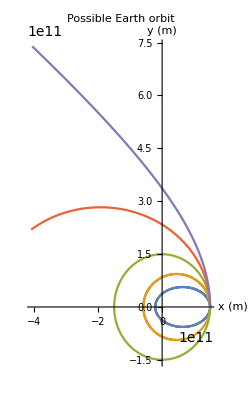

```mathematica
year=24*3600*365.25; (* one year in seconds *)
G=6.6725*10^-11; (* m^3/(kg s^2) *)
au=149597870700; (* m *)
ms=1.989×10^30; (* mass of Sun in kg *)
me=5.972×10^24;  (* mass of Earth in kg *)

(* Without variable localisation *)
earthTrajV[c0_,t_]:=pe[t]/.NDSolve[{
 pe''[t]== - G ms pe[t]/Norm[pe[t]]^3,
pe[0]=={au,0},
pe'[0]=={0,c0 29785.1}},pe,{t,0,3 year},AccuracyGoal->1][[1]]

(* With variable localisation; better programming style *)
earthTrajV[c0_,t_]:=Module[{sol},
sol=NDSolve[{
 pe''[t]== - G ms pe[t]/Norm[pe[t]]^3,
pe[0]=={au,0},
pe'[0]=={0,c0 29785.1}},pe,{t,0,3 year},AccuracyGoal->1][[1]];
pe[t]/.sol]

ParametricPlot[Table[earthTrajV[c0,t],{c0,0.5,1.5,.25}]//Evaluate,{t,0, year},AspectRatio->Automatic,AxesLabel->{"x (m)","y (m)"},PlotLabel->"Possible Earth orbit"]
```

The planet escapes when the initial velocity is 150% of the normal velocity.

-Graphics-

## Planet orbital period function

```mathematica
year=24*3600*365.25; (* one year in seconds *)
G=6.6725*10^-11; (* m^3/(kg s^2) *)
au=149597870700.; (* m *)
ms=1.989×10^30; (* mass of Sun in kg *)
me=5.972×10^24;  (* mass of Earth in kg *)

(* Without variable localisation *)
period[r0_,v0_]:=( NDSolve[{
 pe''[t]== - G ms pe[t]/Norm[pe[t]]^3,
pe[0]=={r0,0},
pe'[0]=={0,v0},WhenEvent[pe[t][[2]]==0&&pe[t][[1]]>0,hit=t;"StopIntegration"]},pe,{t,0,300 year},AccuracyGoal->1];hit)

(* With variable localisation; better programming style *)
period[r0_,v0_]:=Module[{hit,sol},
sol= NDSolve[{
 pe''[t]== - G ms pe[t]/Norm[pe[t]]^3,
pe[0]=={r0,0},
pe'[0]=={0,v0},WhenEvent[pe[t][[2]]==0&&pe[t][[1]]>0,hit=t;"StopIntegration"]},pe,{t,0,300 year},AccuracyGoal->1];
hit]

period[au,29780.1]/year (* orbit period in years *)
```

0.999502

-Graphics-

## Kepler’s Law

{a→5.45733×10^-10,pow→1.49998}

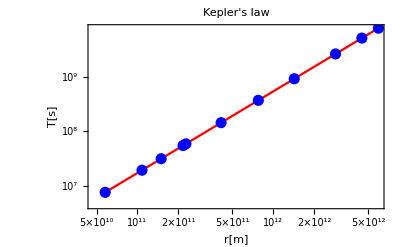

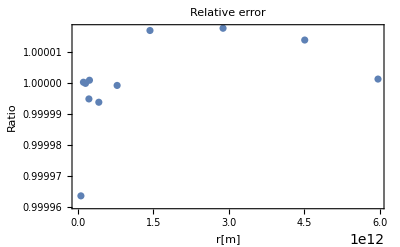

```mathematica
a=.
planetList={{"Mercury",0.38697 au,47880.1},{"Venus",0.722603au,35038.8},{"Earth",au,29785.1},{"asteroid Eros",1.449887au,24736.1},{"Mars",1.522748au,24137.1},{"asteroid Ceres",2.76675au,17906.6},{"Jupiter",5.199940au,13061.7},{"Saturn",9.565644au,9630.4},{"Uranus",19.27835au,6783.7},{"Neptune",30.13411au,5425.9},{"Pluto",39.87356au,4716.9}};

results=Table[{pl[[2]],period[pl[[2]],pl[[3]]]},{pl,planetList}];
kep=Table[{r,2 π Sqrt[r^3/(G ms)]},{r,planetList[[1,2]],planetList[[-1,2]] ,100*^9}];

model=a  r^pow;
fitK=FindFit[results,model,{{a,Exp[-21.5]},{pow,1.508}},r]
ListLogLogPlot[kep,PlotStyle->Red, FrameLabel->{"r[m]","T[s]"},Joined->True,Frame->True,PlotLabel->"Kepler's law",Epilog->{PointSize[0.02],Blue,Point[Log[results]]}]

error=Table[{pl[[2]],period[pl[[2]],pl[[3]]]/(2 π Sqrt[pl[[2]]^3/(G ms)])},{pl,planetList}];
ListPlot[error,FrameLabel->{"r[m]","Ratio"},Frame->True,PlotLabel->"Relative error"]
```

### Retaining planet information with results

If you wanted to retain the planet name information alongside the results, then you can build the results table with this data embedded. However, you must remember it is there remember when you use results, and just extract he bits you want/need. The Apply function can be very useful when manipulating lists. However, it’s application here is quite advanced and you should not worry if you find it unintelligible.

```mathematica
resultswithnames=Table[{pl[[1]],{pl[[2]],period[pl[[2]],pl[[3]]]}},{pl,planetList}];
ListLogLogPlot[kep,PlotStyle->Red, FrameLabel->{"r[m]","T[s]"},Joined->True,Frame->True,PlotLabel->"Kepler's law",Epilog->{PointSize[0.02],Blue,Apply[Tooltip[Point[Log[#2]],#1]&, resultswithnames,{1}]}]
```

-Graphics-